Chiral Fermion Random Circuit |

The modelpaclet:QuantumPlaybook/tutorial/ChiralFermionRandomCircuit#1428088436 | Simulationpaclet:QuantumPlaybook/tutorial/ChiralFermionRandomCircuit#1053215084
Setting up model parameterspaclet:QuantumPlaybook/tutorial/ChiralFermionRandomCircuit#1419497312 | Analysispaclet:QuantumPlaybook/tutorial/ChiralFermionRandomCircuit#2067954741

Here, the effects of random measurements on the entanglement in the Su-Schrieffer-Heeger (SSH) model is investigated. A realization of such chiral fermion random circuit is shown in Figure 1.

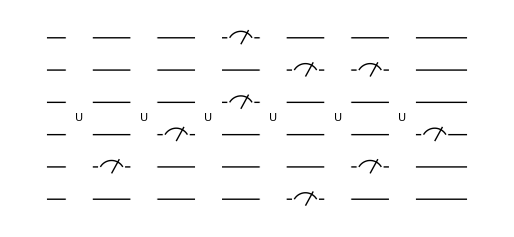

Figure 1. A typical form of chiral fermion random circuit. Each line indicates a fermion mode, the unitary gate with label U denotes the time-evolution of the SSH model, and the measurement symbols depict the measurement of occupation number of the fermion modes.

This demonstration page was motivated by the phenomenon of measurement-induced entanglement transition, a transition between two distinct phases with the entanglement entropy characterized by area- and volume-law scaling. See also Li, Chen, and Fisher (2018)https://doi.org/10.1103%2Fphysrevb.98.205136, Skinner, Ruhman, and Nahum (2019)https://doi.org/10.1103%2Fphysrevx.9.031009, Chan et. al. (2019)https://doi.org/10.1103/PhysRevB.99.224307, Sang et al. (2021)https://doi.org/10.1103/PRXQuantum.2.030313, and Weinstein, Bao, and Altman (2022)https://doi.org/10.1103/PhysRevLett.129.080501.

WickStatepaclet:Q3/ref/WickStateQ3 Package Symbol | Represents a fermionic Gaussian state
WickUnitarypaclet:Q3/ref/WickUnitaryQ3 Package Symbol | Represents a Gaussian-type unitary operator
WickOperatorpaclet:Q3/ref/WickOperatorQ3 Package Symbol | Represents a sequence of linear combinations of Majorana operators
RandomWickCircuitSimulatepaclet:Q3/ref/RandomWickCircuitSimulateQ3 Package Symbol | Rancomd quantum circuit consisting of fermionic gates.
WickGreenFunctionpaclet:Q3/ref/WickGreenFunctionQ3 Package Symbol | Calculates the Green's functions with respect to a Wick state
WickEntanglementEntropypaclet:Q3/ref/WickEntanglementEntropyQ3 Package Symbol | Calculates the entanglement entropy in a Wick state
WickLogarithmicNegativitypaclet:Q3/ref/WickLogarithmicNegativityQ3 Package Symbol | Calculates the logarithmic negativity in a Wick state

Functions for fermionic quantum computation.

The model

In this section, we just examine the model. The material in this section is not directly used in the demonstration from the next section and on. If you are already familiar with the model, you can skip this part.

Make sure to load Q3.

```mathematica
<<Q3`
```

The bare fermion modes.

```mathematica
Let[Fermion,c]
```

Consider a system of n fermion modes.

```mathematica
$n=6;
cc=c[Range@$n]
odd=cc[[1;;;;2]]
evn=cc[[2;;;;2]]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6)}

{c_(,,1),c_(,,3),c_(,,5)}

{c_(,,2),c_(,,4),c_(,,6)}

Construct the many-body Hamiltonian of the SSH model.

```mathematica
Let[Real,g]
```

```mathematica
HH=-g[1]*Hop[{odd,evn}]-g[2]*Hop[{Most@evn,Rest@odd}]
HH=HH//PlusDagger;
```

-g_(,,2) (c_(,,2)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,5))-g_(,,1) (c_(,,1)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,4)+c_(,,5)^(,,†)c_(,,6))

Examine the connectivity between neighboring fermion modes.

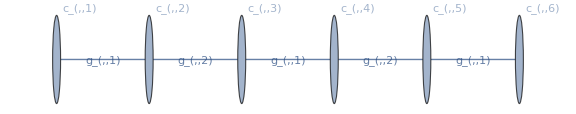

```mathematica
GraphForm[-HH]
```

Extract the single-particle (or Bogoliubov-de Gennes) Hamiltonian (cf. many-body Hamiltonian in the above) of the model in the Nambu space.

```mathematica
matH=CoefficientTensor[HH,Dagger@cc,cc];
ArrayShort[matH,"Size"->8]
```

(0 | -g_(,,1) | 0 | 0 | 0 | 0
-g_(,,1) | 0 | -g_(,,2) | 0 | 0 | 0
0 | -g_(,,2) | 0 | -g_(,,1) | 0 | 0
0 | 0 | -g_(,,1) | 0 | -g_(,,2) | 0
0 | 0 | 0 | -g_(,,2) | 0 | -g_(,,1)
0 | 0 | 0 | 0 | -g_(,,1) | 0)

Rearrange the rows and columns so that the chiral symmetry of the model becomes clearer; that is, the single-particle Hamiltonian in the block off-diagonal form.

```mathematica
chi=CoefficientTensor[HH,Dagger@Join[odd,evn],Join[odd,evn]];
ArrayShort[chi,"Size"->8]
```

(0 | 0 | 0 | -g_(,,1) | 0 | 0
0 | 0 | 0 | -g_(,,2) | -g_(,,1) | 0
0 | 0 | 0 | 0 | -g_(,,2) | -g_(,,1)
-g_(,,1) | -g_(,,2) | 0 | 0 | 0 | 0
0 | -g_(,,1) | -g_(,,2) | 0 | 0 | 0
0 | 0 | -g_(,,1) | 0 | 0 | 0)

Any physical properties of the model is completely determined by the off-diagonal blocks.

```mathematica
chi=CoefficientTensor[HH,Dagger@odd,evn];
chi//ArrayShort
```

(-g_(,,1) | 0 | 0
-g_(,,2) | -g_(,,1) | 0
0 | -g_(,,2) | -g_(,,1))

Re-examine the connectivity of the fermionic modes in the model.

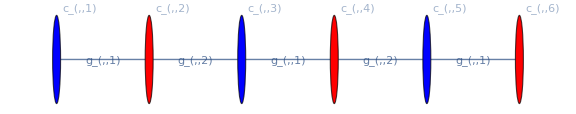

```mathematica
ChiralGraphForm[-chi,VertexLabels->{odd,evn}]
```

Setting up model parameters

Now, we set up the parameters for the demonstration.

Make sure to load Q3.

```mathematica
<<Q3`
```

Set the number of fermion modes to consider.

```mathematica
$n=10;
```

Directly construct the single-particle Hamiltonian of the SSH model (without using fermion operator algebra as in the above).

```mathematica
Let[Real,g]
```

```mathematica
matH=PadRight[g@{1,2},$n-1,g@{1,2}];
matH=PlusTopple@DiagonalMatrix[-matH,1];
ArrayShort[matH,"Size"->6]
```

(0 | -g_(,,1) | 0 | 0 | 0 | 0 | …
-g_(,,1) | 0 | -g_(,,2) | 0 | 0 | 0 | …
0 | -g_(,,2) | 0 | -g_(,,1) | 0 | 0 | …
0 | 0 | -g_(,,1) | 0 | -g_(,,2) | 0 | …
0 | 0 | 0 | -g_(,,2) | 0 | -g_(,,1) | …
0 | 0 | 0 | 0 | -g_(,,1) | 0 | …
… | … | … | … | … | … | …)

```mathematica
ham=NambuHermitian[{matH,0}]
ham//ArrayShort
```

NambuHermitian[…]

{(0 | -g_(,,1) | 0 | 0 | …
-g_(,,1) | 0 | -g_(,,2) | 0 | …
0 | -g_(,,2) | 0 | -g_(,,1) | …
0 | 0 | -g_(,,1) | 0 | …
… | … | … | … | …),(0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
0 | 0 | 0 | 0 | …
… | … | … | … | …)}

Convert the above Hamiltonian matrix in the Dirac spinor space to that in the Majorana spinor space.

```mathematica
ant=WickHermitian[ham]
ant//ArrayShort
```

WickHermitian[…]

(0 | 0 | 0 | -g_(,,1) | …
0 | 0 | g_(,,1) | 0 | …
0 | -g_(,,1) | 0 | 0 | …
g_(,,1) | 0 | 0 | 0 | …
… | … | … | … | …)

The time interval for each unitary layer to operate.

```mathematica
$τ=0.5;
```

The alternating hopping amplitudes.

```mathematica
$g1=1;
$g2=10.;
```

Construct the single-particle time-evolution matrix.

```mathematica
matR=MatrixExp[Normal[ant]/.{g[1]->$g1,g[2]->$g2}];
matR//ArrayShort
```

(0.982554 | 0 | 0 | 0.0487848 | …
0 | 0.982554 | -0.0487848 | 0 | …
0 | 0.0487848 | -0.719599 | 0 | …
-0.0487848 | 0 | 0 | -0.719599 | …
… | … | … | … | …)

Construct the corresponding unitary (in fact, real orthogonal) matrix. It has the same information as the above matrix, but operates directly on Wick states.

```mathematica
wu=WickUnitary[matR,"Label"->"R"]
```

WickUnitary[…]

Prepare an initial state. A half-filling is a common choice.

```mathematica
in=WickState[{1,0},$n]
```

WickState[…]

The probability to perform a measurement on each fermion mode.

```mathematica
$p=.2;
```

The depth of quantum circuit.

```mathematica
$T=20; (* must be an integer *)
```

Simulation

The simulation involves a lot of random number generators. To get the same result every time you open this document, set the seed of the random number generator.

```mathematica
SeedRandom[361];(*for tests*)
```

Construct 20 random circuits and run each circuit 5 times. Notice the "Samples"→{20,5} option.

```mathematica
EchoTiming[
{data,qc}=RandomWickCircuitSimulate[in,{wu,$p},$T,
"Samples"->{200,2}]
];
```

3.63114

Examine the output data format: There are 10 entries because the same number of quantum circuits were randomly generated.

```mathematica
Length[qc]
```

200

```mathematica
Dimensions[data]
```

{200,2,41}

If you want, examine the circuits by displaying them in a graphical form.

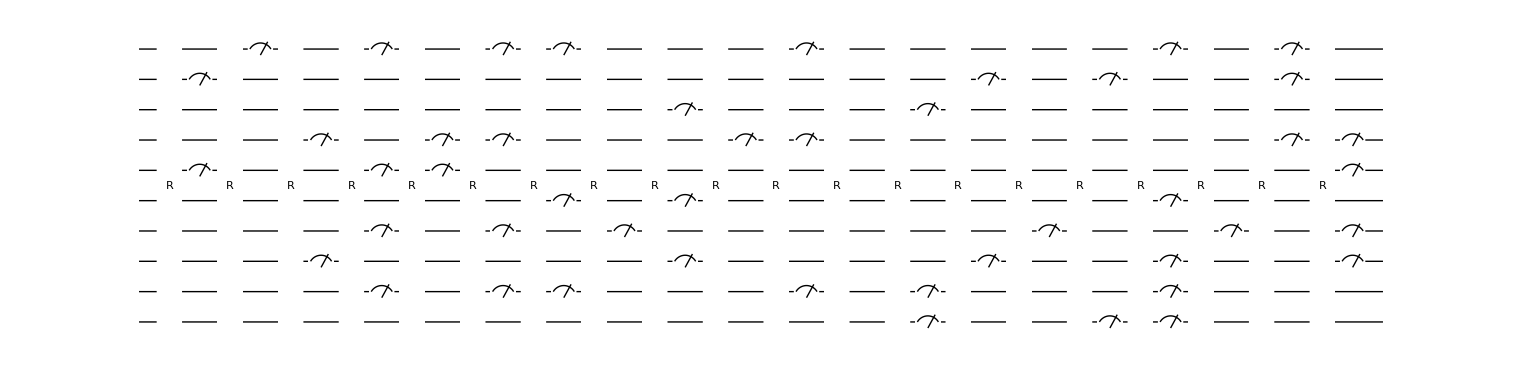

```mathematica
Show[qc[[2]]]
```

Examine some of the output states as well.

```mathematica
out=data[[2,2,3]]
```

WickState[…]

Analysis

Each entry in the  data contains the information about one realization of quantum trajectory. Extract the trajectory history in an explicit form, for example, of the first entry.

```mathematica
trj=Flatten[data,1][[;;,1;;;;2]];
```

In this particular case, there are 13 entries; the first entry is just the initial state and the rest are corresponds to the layers; there are 6 layers and each layer contains two sub-layers of unitary evolution and measurements.

```mathematica
Dimensions[trj]
```

{400,21}

Note that the output states are all normalized.

```mathematica
EchoTiming[nrm=Map[NormSquare,trj,{2}];]
ArrayShort[nrm//IntegerChop]
```

0.015778

(1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
… | … | … | … | …)

```mathematica
nrm-1//ArrayZeroQ
```

True

### Entanglement Entropy

Take a subsystem containing the first half of the whole modes.

```mathematica
aa=Range[$n/2]
```

{1,2,3,4,5}

Calculate the entanglement entropy, and take the average over different trajectories.

```mathematica
EchoTiming[
ee=Re@WickEntanglementEntropy[trj,aa]
];
```

1.76706

Plot the entanglement entropy (EE)  as a function of time.

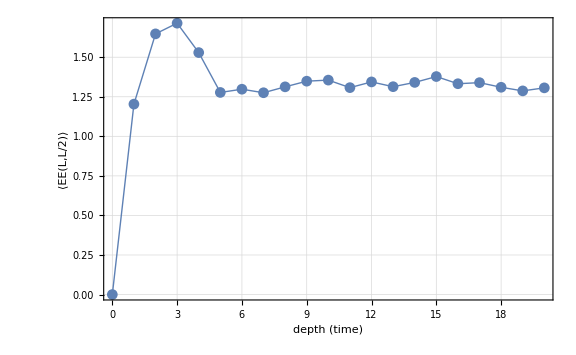

```mathematica
ListLinePlot[Mean@ee,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "⟨EE(L,L/2)⟩"}]
```

### Entanglement Entropy: For different sub-system sizes

Now, let us examine the entanglement entropy for subsystems of different sizes. The largest subsystem has a half of the whole modes.

```mathematica
aa=Range[$n/2]
```

{1,2,3,4,5}

From the Green’s functions, calculate the entanglement entropy for different subsystems, taking the average over all quantum trajectories.

```mathematica
EchoTiming[
ees=Table[
kk=Range[k];
Re@Mean@WickEntanglementEntropy[trj,kk],
{k,$n/2}
]
];
```

6.66926

```mathematica
Dimensions[ees]
```

{5,21}

Plot the average entanglement entropy (EE) as a function of time.

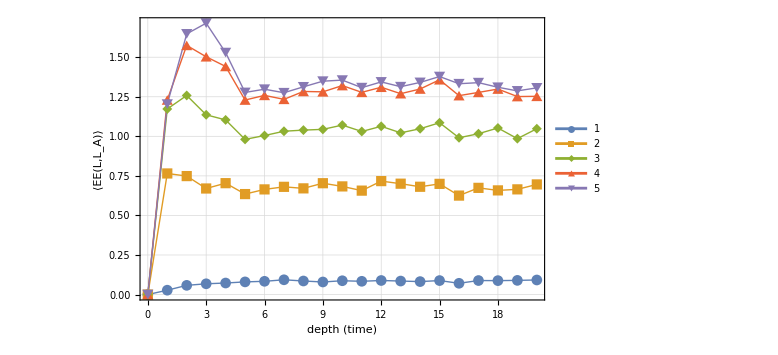

```mathematica
ListLinePlot[ees,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
PlotLegends->Automatic,
FrameLabel->{"depth (time)", "⟨EE(L,L_A)⟩"}]
```

### Green's Functions

N.B. Since Q3 v3.7.0, it is not necessary to calculate the Green's functions since the output state in the WickStatepaclet:Q3/ref/WickStateQ3 Package Symbol object already contains the equivalent Majorana covariance matrix.

Calculate the Green's functions.

```mathematica
EchoTiming[grn=WickGreenFunction[trj]];
```

1.08324

```mathematica
Dimensions[grn]
```

{400,21}

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪B. M. Terhal and D. P. DiVincenzo (2002)https://doi.org/10.1103/PhysRevA.65.032325, Physical Review A 65, 032325, "Classical simulation of noninteracting-fermion quantum circuits."
▪A. Yu. Kitaev (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, Physics-Uspekhi 44, 131 (2001), "Unpaired Majorana fermions in quantum wires." 
▪Y. Li, X. Chen, and M. P. A. Fisher (2018)https://doi.org/10.1103%2Fphysrevb.98.205136, Physical Review B 98, 205136 (2018), "Quantum Zeno effect and the many-body entanglement transition."
▪B. Skinner, J. Ruhman, and A. Nahum (2019)https://doi.org/10.1103%2Fphysrevx.9.031009, Physical Review X 9, 031009 (2019), "Measurement-Induced Phase Transitions in the Dynamics of Entanglement."
▪A. Chan et. al. (2019)https://doi.org/10.1103/PhysRevB.99.224307, Physical Review B 99, 224307 (2019), "Unitary-projective entanglement dynamics."
▪S. Sang et al. (2021)https://doi.org/10.1103/PRXQuantum.2.030313, PRX Quantum 2, 030313 (2021), "Entanglement Negativity at Measurement-Induced Criticality."
▪Z. Weinstein, Y. Bao, and E. Altman (2022)https://doi.org/10.1103/PhysRevLett.129.080501, Physical Review Letters 129, 080501 (2022), "Measurement-Induced Power-Law Negativity in an Open Monitored Quantum Circuit."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
▪About Q3